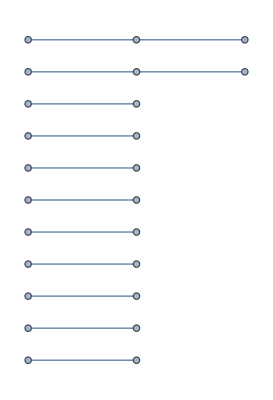
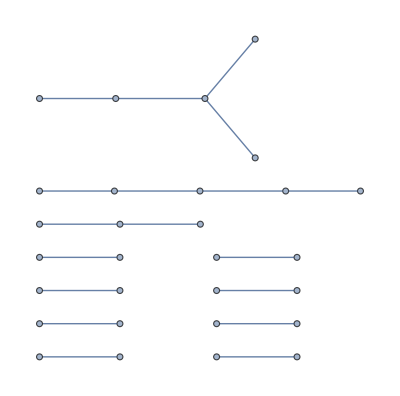
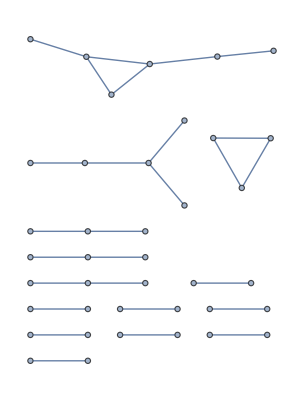
```mathematica
#!/usr/local/bin/MathematicaScript-script

(*directory="/Users/d1795494/Documents/PIPELINE/MitoGFP/";*)
directory=$ScriptCommandLine[[2]];
(*toSetDirectory="/Users/d1795494/Documents/PIPELINE/MitoGFP/ScaleAndCrop-goodvid120";*)
toSetDirectory= ""<>ToString[$ScriptCommandLine[[2]]]<>""<>ToString[$ScriptCommandLine[[3]]]<>"";
SetDirectory[toSetDirectory];
(*name="ScaleAndCrop-goodvid120";*)
name=$ScriptCommandLine[[3]];
(*resultsfilename="goodvid120ADJUSTEDCROPPEDabs0-9.csv";*)
resultsfilename = $ScriptCommandLine[[4]];
(*colocdist="8.0";*)
colocdist=$ScriptCommandLine[[8]];
(*indexlist=Range[1,3];*)
indexlist = Range[1, ToExpression[$ScriptCommandLine[[7]]]];
graphlist={};
For[ k=1,k≤Length[indexlist],k++,
networkdata= ReadList[""<>ToString[directory]<>""<>ToString[name]<>"/"<>ToString[resultsfilename]<>"-"<>ToString[colocdist]<>"-"<>ToString[indexlist[[k]]]<>".txt",{Number,Number}];
am=Table[networkdata[[i]][[1]]->networkdata[[i]][[2]],{i,1,Length[networkdata]}];
amf=Table[networkdata[[i]][[1]]<->networkdata[[i]][[2]],{i,1,Length[networkdata]}];
graph=Graph[amf];
graphlist=Append[graphlist,graph];
]
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
WalkerDegreeDropx5[x_]:=Module[{graph=x},
(*start is The first node in the walk chain, we use Pick to choose the vertex with the highest degree centrality and start from there*)
start=Pick[VertexList[graph],DegreeCentrality[graph],Max[DegreeCentrality[graph]]];
start=start[[1]];
myTable={};
myNormTable={};
(*loop over the walked path 2000 times to average the degree drop over*)
For[m=1,m≤200,m++,
(*step randomly 10 times from the start vertex*)
randompath=NestList[RandomChoice[AdjacencyList[graph,#]]&,start,10];
pathlist={};
normpathlist={};
For[ p=1,p≤Length[randompath],p++, 
(*get the degree value of each vertex you stepped on*)
degreeValue=Pick[DegreeCentrality[graph],VertexList[graph],randompath[[p]]];
(*add to the non-normalised list*)
pathlist=Append[pathlist,degreeValue];
(*normalise it by the number of vertices in the graph*)
normDegreeValue=N[degreeValue/VertexCount[graph]];
(*add to the normalised list*)
normpathlist=Append[normpathlist,normDegreeValue];
]
AppendTo[myNormTable, Flatten[normpathlist]];
AppendTo[myTable, Flatten[pathlist]];
]
]
```

```mathematica
meanDroplistStartTo5th={};
meanDroplist5thTo10th={};
meanDroplistStartTo10th={};
For[ g=1,g≤Length[graphlist],g++,
(*For all the graphs (one for each frame, run them through the walker degree drop function, and store their node degrees by step, as well as the drops between 1-5 5-10 and 1-10 steps*)
WalkerDegreeDropx5[graphlist[[g]]];
Export[ "NormalisedWalkerDegreeTableByStepFrame"<>ToString[indexlist[[g]]]<>".csv",Prepend[myNormTable,{"HighestDegree","Step1","Step2","Step3","Step4","Step5","Step6","Step7","Step8","Step9","Step10"}]];
Export[ "WalkerDegreeTableByStepFrame"<>ToString[indexlist[[g]]]<>".csv",Prepend[myTable,{"HighestDegree","Step1","Step2","Step3","Step4","Step5","Step6","Step7","Step8","Step9","Step10"}]];

(*This is for picking out the columns, this below picks the degree of 1st colum(max degree node), 6th column(5th random walk site), 11th column(10th random walk site)*)
firstandfifth=myNormTable[[All,{1}]]-myNormTable[[All,{6}]];
fifthandtenth=myNormTable[[All,{6}]]-myNormTable[[All,{11}]];
firstandtenth=myNormTable[[All,{1}]]-myNormTable[[All,{11}]];
(*Then we take the mean of all the many iteractions,for specific walker degree drops*)
meanDroplistStartTo5th=Append[meanDroplistStartTo5th,Mean[firstandfifth]];
meanDroplist5thTo10th=Append[meanDroplist5thTo10th,Mean[fifthandtenth]];
meanDroplistStartTo10th=Append[meanDroplistStartTo10th,Mean[firstandtenth]];
]
meanDropListTable=List[Flatten[indexlist],Flatten[meanDroplistStartTo5th],Flatten[meanDroplist5thTo10th],Flatten[meanDroplistStartTo10th]];
Export["MeanDropsBetweenStepsForAllFramesIn"<>ToString[name]<>".csv",Prepend[Transpose[meanDropListTable],{"Frame","DropbetweenStartand5th","Dropbetween5stand10th","DropbetweenStartand10th"}]//TableForm];
```